```mathematica
SetDirectoryToNotebookLocation[];
```

```mathematica
Needs["DatabaseLink`"];
Needs["Graphics`MultipleListPlot`"]
```

```mathematica
getLearnToCrit[filename_]:=Module[
{data,cond,shjtype,blockstocrit},
data=Import[filename,"CSV"];
cond=data[[1]][[2]];
shjtype=data[[1]][[3]];
blockstocrit=Max[Select[Select[data,Length[#]>6&][[All,6]],NumberQ]];
{{cond,shjtype},blockstocrit}
];

getLCurve[fn_]:=Module[
{data,errorcurve,i,cond,shjtype,blockscore},
data=Import[fn,"CSV"];
cond=data[[1]][[2]];
shjtype=data[[1]][[3]];
data=Select[data,Length[#]>8&];
errorcurve={};
For[i=1,i≤20,i++,
blockscore=Select[data,(#[[8]]=="TEST")&&(#[[6]]==i)&][[All,-2]]/.{"false"->1,"true"->0};
AppendTo[errorcurve,If[blockscore=={},0.0,N[Mean[blockscore]]]];
];
{{cond,shjtype},errorcurve}
];

getMeanBlocks[data_,cond_]:=Module[
{part},
part=Select[data,#[[1,1,2]]==cond&][[All,All,-1]];
If[part≠{},N[Mean[part[[1]]]],0]
];


getMeanBlocks2[data_,cond_]:=Module[
{part},
part=Select[data,#[[1,1,2]]==cond&][[All,All,-1]];
If[part≠{},N[Mean[Select[part[[1]],#<20&]]],0]
];

getNSubj[data_,cond_]:=Module[
{part},
part=Select[data,#[[1,1,2]]==cond&][[All,All,-1]];
If[part≠{},Length[part[[1]]],0]
];

getAverageLCurve[data_,cond_]:=Module[
{part},
part=Select[data,#[[1,1,2]]==cond&][[All,All,-1]];
If[part≠{},Mean/@Transpose[part[[1]]],Table[1.0,{20}]]
];
```

## Open database and save data to disk

```mathematica
conn=OpenSQLConnection[JDBC["MySQL(Connector/J)","gureckislab.org:3306/active_learn_shj_turk"],"Username"->"lab","Password"->"2research"];
```

```mathematica
res=SQLSelect[conn,"participants_v2",
{"subjid","hitid","cond","assignmentid","beginhit","endhit","status","debriefed","datafile"},(SQLColumn["endhit"]≠Null)&&(SQLColumn["debriefed"]==1)&&(SQLColumn["codeversion"]=="2.0")&&SQLColumn["status"]≥3];
```

```mathematica
savedata[sn_,data_]:=Export[StringJoin[{"data_v2/",ToString[sn],".txt"}],data,"String"];
fns=(savedata[#[[1]],#[[-1]]])&/@res
Length[fns]
```

{data_v2/306.txt,data_v2/307.txt,data_v2/308.txt,data_v2/309.txt,data_v2/310.txt,data_v2/311.txt,data_v2/312.txt,data_v2/313.txt,data_v2/314.txt}

9

```mathematica
{#,StringSplit[Import[#,"CSV"][[-1,1]],":"][[-1]]}&/@fns;
fns2v2=Select[%,#[[-1]]=="no"&][[All,1]]
```

{data_v2/306.txt,data_v2/307.txt,data_v2/308.txt,data_v2/309.txt,data_v2/310.txt,data_v2/311.txt,data_v2/313.txt,data_v2/314.txt}

```mathematica
Length[fns2]
```

8

```mathematica
Import[fns[[2]],"CSV"]
```

{{4,0,2,6,15,INSTRUCT,instruct1,11710},{4,0,2,6,15,INSTRUCT,instructCatExample,7078},{4,0,2,6,15,INSTRUCT,instructCatColor,4013},{4,0,2,6,15,INSTRUCT,instructCatStripe,4215},{4,0,2,6,15,INSTRUCT,instructDemoIntro,6019},{4,0,2,6,15,INSTRUCT,instructDemo,29273},{4,0,2,6,15,INSTRUCT,instructTest,8571},{4,0,2,6,15,INSTRUCT,instructTest2,1398},{4,0,2,6,15,INSTRUCT,instructDimColor,4486},{4,0,2,6,15,INSTRUCT,instructDimBorder,3445},{4,0,2,6,15,INSTRUCT,instructDimDots,1645},{4,0,2,6,15,INSTRUCT,instructDimStripe,1984},{4,0,2,6,15,INSTRUCT,instructDimAll,6161},{4,0,2,6,15,INSTRUCT,instructFinal,11174},{4,0,2,6,15,1,1,TRAINING,2,11,1,2,75246301,15b739fd,3198},{4,0,2,6,15,1,2,TRAINING,2,11,1,2,75264301,15b379fd,2321},{4,0,2,6,15,1,3,TRAINING,7,1,0,0,70264351,1fb3795d,1362},{4,0,2,6,15,1,4,TRAINING,7,1,0,0,70265341,1fb3597d,3952},{4,0,2,6,15,1,5,TRAINING,3,9,0,4,70263541,1fb3957d,3194},{4,0,2,6,15,1,6,TRAINING,4,7,1,6,76203541,13bf957d,3889},{4,0,2,6,15,1,7,TRAINING,5,5,1,5,16203547,d3bf9571,945},{4,0,2,6,15,1,8,TRAINING,2,11,1,2,17203546,d1bf9573,1977},{4,0,2,6,15,1,9,TRAINING,0,15,1,3,47203516,71bf95d3,1737},{4,0,2,6,15,1,10,TRAINING,4,7,1,0,47203561,71bf953d,1858},{4,0,2,6,15,1,11,TRAINING,1,13,0,7,47203651,71bf935d,1440},{4,0,2,6,15,1,12,TRAINING,5,5,1,6,42703651,7b1f935d,1082},{4,0,2,6,15,1,13,TRAINING,4,7,1,5,62703451,3b1f975d,1153},{4,0,2,6,15,1,14,TRAINING,4,7,1,5,26703451,b31f975d,6067},{4,0,2,6,15,1,15,TRAINING,6,3,0,1,26705431,b31f579d,928},{4,0,2,6,15,1,16,TRAINING,4,7,1,5,26305471,b39f571d,1018},{4,0,2,6,15,1,17,TEST,3,9,0,0,true,1367},{4,0,2,6,15,1,18,TEST,6,3,0,1,false,1627},{4,0,2,6,15,1,19,TEST,1,13,0,1,false,1290},{4,0,2,6,15,1,20,TEST,5,5,1,1,true,665},{4,0,2,6,15,1,21,TEST,4,7,1,1,true,619},{4,0,2,6,15,1,22,TEST,7,1,0,0,true,522},{4,0,2,6,15,1,23,TEST,2,11,1,1,true,863},{4,0,2,6,15,1,24,TEST,0,15,1,1,true,619},{4,0,2,6,15,2,25,TRAINING,7,1,0,0,72534160,1b597d3f,2842},{4,0,2,6,15,2,26,TRAINING,4,7,1,4,72354160,1b957d3f,1796},{4,0,2,6,15,2,27,TRAINING,2,11,1,1,72654130,1b357d9f,1216},{4,0,2,6,15,2,28,TRAINING,1,13,0,6,72654310,1b3579df,1058},{4,0,2,6,15,2,29,TRAINING,6,3,0,2,72654013,1b357fd9,929},{4,0,2,6,15,2,30,TRAINING,5,5,1,3,74652013,1735bfd9,6529},{4,0,2,6,15,2,31,TRAINING,6,3,0,2,74652031,1735bf9d,1290},{4,0,2,6,15,2,32,TRAINING,4,7,1,1,74652301,1735b9fd,3531},{4,0,2,6,15,2,33,TRAINING,0,15,1,0,4652371,f735b91d,1369},{4,0,2,6,15,2,34,TRAINING,1,13,0,7,4672351,f731b95d,1217},{4,0,2,6,15,2,35,TRAINING,3,9,0,6,4672531,f731b59d,2247},{4,0,2,6,15,2,36,TRAINING,5,5,1,5,6472531,f371b59d,6043},{4,0,2,6,15,2,37,TRAINING,0,15,1,7,16472530,d371b59f,1520},{4,0,2,6,15,2,38,TRAINING,7,1,0,3,16473520,d37195bf,1203},{4,0,2,6,15,2,39,TRAINING,6,3,0,0,61473520,3d7195bf,1409},{4,0,2,6,15,2,40,TRAINING,2,11,1,6,61374520,3d9175bf,1176},{4,0,2,6,15,2,41,TEST,0,15,1,1,true,1607},{4,0,2,6,15,2,42,TEST,1,13,0,0,true,458},{4,0,2,6,15,2,43,TEST,7,1,0,0,true,993},{4,0,2,6,15,2,44,TEST,6,3,0,1,false,442},{4,0,2,6,15,2,45,TEST,4,7,1,1,true,326},{4,0,2,6,15,2,46,TEST,3,9,0,0,true,441},{4,0,2,6,15,2,47,TEST,2,11,1,1,true,338},{4,0,2,6,15,2,48,TEST,5,5,1,0,false,394},{4,0,2,6,15,3,49,TRAINING,0,15,1,0,3761524,f913d5b7,4506},{4,0,2,6,15,3,50,TRAINING,3,9,0,1,3261574,f9b3d517,914},{4,0,2,6,15,3,51,TRAINING,2,11,1,2,3265174,f9b35d17,826},{4,0,2,6,15,3,52,TRAINING,1,13,0,3,3215674,f9bd5317,1217},{4,0,2,6,15,3,53,TRAINING,5,5,1,4,6215374,f3bd5917,2449},{4,0,2,6,15,3,54,TRAINING,7,1,0,5,6215734,f3bd5197,970},{4,0,2,6,15,3,55,TRAINING,4,7,1,2,6415732,f37d519b,930},{4,0,2,6,15,3,56,TRAINING,3,9,0,6,1465732,fd73519b,1457},{4,0,2,6,15,3,57,TRAINING,7,1,0,7,1465237,fd735b91,1186},{4,0,2,6,15,3,58,TRAINING,2,11,1,0,21465037,bd735f91,2160},{4,0,2,6,15,3,59,TRAINING,4,7,1,2,26415037,b37d5f91,1873},{4,0,2,6,15,3,60,TRAINING,3,9,0,3,26435017,b3795fd1,1425},{4,0,2,6,15,3,61,TRAINING,1,13,0,1,21435067,bd795f31,1538},{4,0,2,6,15,3,62,TRAINING,0,15,1,6,21435607,bd7953f1,1682},{4,0,2,6,15,3,63,TRAINING,2,11,1,5,61435207,3d795bf1,1505},{4,0,2,6,15,3,64,TRAINING,1,13,0,1,61475203,3d715bf9,4353},{4,0,2,6,15,3,65,TEST,1,13,0,0,true,710},{4,0,2,6,15,3,66,TEST,7,1,0,0,true,1097},{4,0,2,6,15,3,67,TEST,0,15,1,1,true,1384},{4,0,2,6,15,3,68,TEST,4,7,1,0,false,1914},{4,0,2,6,15,3,69,TEST,6,3,0,0,true,659},{4,0,2,6,15,3,70,TEST,5,5,1,1,true,1554},{4,0,2,6,15,3,71,TEST,3,9,0,0,true,394},{4,0,2,6,15,3,72,TEST,2,11,1,0,false,411},{4,0,2,6,15,4,73,TRAINING,5,5,1,0,53746102,59173dfb,14172},{4,0,2,6,15,4,74,TRAINING,5,5,1,0,53742106,5917bdf3,920},{4,0,2,6,15,4,75,TRAINING,5,5,1,0,53472106,5971bdf3,466},{4,0,2,6,15,4,76,TRAINING,7,1,0,1,57432106,5179bdf3,7105},{4,0,2,6,15,4,77,TRAINING,1,13,0,2,57132406,51d9b7f3,3521},{4,0,2,6,15,4,78,TRAINING,1,13,0,2,37152406,91d5b7f3,3703},{4,0,2,6,15,4,79,TRAINING,5,5,1,3,47152306,71d5b9f3,5986},{4,0,2,6,15,4,80,TRAINING,4,7,1,0,47150326,71d5f9b3,7457},{4,0,2,6,15,4,81,TRAINING,4,7,1,0,43150726,79d5f1b3,8578},{4,0,2,6,15,4,82,TRAINING,6,3,0,7,47150326,71d5f9b3,2183},{4,0,2,6,15,4,83,TRAINING,2,11,1,6,47130526,71d9f5b3,5898},{4,0,2,6,15,4,84,TRAINING,3,9,0,3,57130426,51d9f7b3,18081},{4,0,2,6,15,4,85,TRAINING,0,15,1,4,17530426,d159f7b3,9401},{4,0,2,6,15,4,86,TRAINING,7,1,0,1,17530624,d159f3b7,9242},{4,0,2,6,15,4,87,TRAINING,5,5,1,2,67530124,3159fdb7,2979},{4,0,2,6,15,4,88,TRAINING,5,5,1,2,67531024,3159dfb7,3234},{4,0,2,6,15,4,89,TEST,3,9,0,1,false,4255},{4,0,2,6,15,4,90,TEST,0,15,1,1,true,4587},{4,0,2,6,15,4,91,TEST,5,5,1,1,true,3508},{4,0,2,6,15,4,92,TEST,2,11,1,1,true,3042},{4,0,2,6,15,4,93,TEST,1,13,0,0,true,3794},{4,0,2,6,15,4,94,TEST,4,7,1,1,true,1866},{4,0,2,6,15,4,95,TEST,6,3,0,0,true,2060},{4,0,2,6,15,4,96,TEST,7,1,0,0,true,1499},{4,0,2,6,15,5,97,TRAINING,5,5,1,0,54130762,57d9f13b,44075},{4,0,2,6,15,5,98,TRAINING,4,7,1,1,54130267,57d9fb31,7817},{4,0,2,6,15,5,99,TRAINING,1,13,0,2,54132067,57d9bf31,5441},{4,0,2,6,15,5,100,TRAINING,3,9,0,5,54102367,57dfb931,4384},{4,0,2,6,15,5,101,TRAINING,0,15,1,3,56102347,53dfb971,5346},{4,0,2,6,15,5,102,TRAINING,7,1,0,7,65102347,35dfb971,3898},{4,0,2,6,15,5,103,TRAINING,6,3,0,0,65201347,35bfd971,4953},{4,0,2,6,15,5,104,TRAINING,2,11,1,2,63201547,39bfd571,3370},{4,0,2,6,15,5,105,TRAINING,7,1,0,7,63204517,39bf75d1,2521},{4,0,2,6,15,5,106,TRAINING,1,13,0,6,64203517,37bf95d1,1003},{4,0,2,6,15,5,107,TRAINING,6,3,0,4,34206517,97bf35d1,1160},{4,0,2,6,15,5,108,TRAINING,2,11,1,2,30246517,9fb735d1,937},{4,0,2,6,15,5,109,TRAINING,6,3,0,4,30276514,9fb135d7,1073},{4,0,2,6,15,5,110,TRAINING,4,7,1,7,3276514,f9b135d7,1738},{4,0,2,6,15,5,111,TRAINING,6,3,0,4,7236514,f1b935d7,930},{4,0,2,6,15,5,112,TRAINING,2,11,1,2,1236574,fdb93517,1505},{4,0,2,6,15,5,113,TEST,5,5,1,1,true,3199},{4,0,2,6,15,5,114,TEST,0,15,1,1,true,5692},{4,0,2,6,15,5,115,TEST,1,13,0,0,true,2641},{4,0,2,6,15,5,116,TEST,4,7,1,1,true,3878},{4,0,2,6,15,5,117,TEST,7,1,0,0,true,4746},{4,0,2,6,15,5,118,TEST,3,9,0,0,true,3738},{4,0,2,6,15,5,119,TEST,6,3,0,0,true,7256},{4,0,2,6,15,5,120,TEST,2,11,1,1,true,4373},{4,0,2,6,15,6,121,TRAINING,7,1,0,0,71650234,1d35fb97,75571},{4,0,2,6,15,6,122,TRAINING,1,13,0,1,71620534,1d3bf597,3961},{4,0,2,6,15,6,123,TRAINING,6,3,0,2,71623504,1d3b95f7,3825},{4,0,2,6,15,6,124,TRAINING,6,3,0,2,71624503,1d3b75f9,8090},{4,0,2,6,15,6,125,TRAINING,5,5,1,5,71604523,1d3f75b9,1497},{4,0,2,6,15,6,126,TRAINING,0,15,1,7,71634520,1d3975bf,3867},{4,0,2,6,15,6,127,TRAINING,2,11,1,6,41637520,7d3915bf,2304},{4,0,2,6,15,6,128,TRAINING,3,9,0,3,41635720,7d3951bf,3417},{4,0,2,6,15,6,129,TRAINING,4,7,1,1,14635720,d73951bf,2403},{4,0,2,6,15,6,130,TRAINING,6,3,0,6,14235760,d7b9513f,5833},{4,0,2,6,15,6,131,TRAINING,4,7,1,1,14035762,d7f9513b,1570},{4,0,2,6,15,6,132,TRAINING,3,9,0,3,54031762,57f9d13b,1497},{4,0,2,6,15,6,133,TRAINING,2,11,1,7,54731062,5719df3b,2345},{4,0,2,6,15,6,134,TRAINING,0,15,1,6,54731602,5719d3fb,2025},{4,0,2,6,15,6,135,TRAINING,7,1,0,1,57431602,5179d3fb,2848},{4,0,2,6,15,6,136,TRAINING,1,13,0,4,57461302,5173d9fb,1875},{4,0,2,6,15,6,137,TEST,5,5,1,1,true,5364},{4,0,2,6,15,6,138,TEST,0,15,1,1,true,3507},{4,0,2,6,15,6,139,TEST,7,1,0,0,true,2509},{4,0,2,6,15,6,140,TEST,3,9,0,0,true,2442},{4,0,2,6,15,6,141,TEST,6,3,0,0,true,7204},{4,0,2,6,15,6,142,TEST,4,7,1,1,true,5521},{4,0,2,6,15,6,143,TEST,1,13,0,0,true,10217},{4,0,2,6,15,6,144,TEST,2,11,1,1,true,3535},{4,0,2,6,15,INSTRUCT,postquestionnaire,3},{},{rulestrategy:I took mental notes until I understood the categories.},{howtoimprove:},{engagement:5},{difficulty:5},{:no}}

```mathematica
{#,StringSplit[Import[#,"CSV"][[-3,1]],":"][[-1]]}&/@fns
```

{{data/3.txt,8},{data/4.txt,5},{data/7.txt,7},{data/8.txt,8},{data/10.txt,9},{data/13.txt,9},{data/21.txt,10},{data/23.txt,7},{data/24.txt,10},{data/25.txt,10},{data/26.txt,9},{data/27.txt,8},{data/29.txt,10},{data/30.txt,10},{data/31.txt,10},{data/32.txt,10},{data/34.txt,8},{data/35.txt,10},{data/37.txt,10},{data/38.txt,7},{data/39.txt,9},{data/40.txt,10},{data/41.txt,10},{data/42.txt,10},{data/45.txt,9},{data/46.txt,10},{data/50.txt,8},{data/53.txt,8},{data/54.txt,10},{data/55.txt,10},{data/57.txt,8},{data/58.txt,10},{data/62.txt,9},{data/65.txt,10},{data/66.txt,10},{data/69.txt,8},{data/70.txt,10},{data/73.txt,10},{data/74.txt,10},{data/75.txt,8},{data/76.txt,9},{data/79.txt,0},{data/80.txt,9},{data/82.txt,4},{data/84.txt,9},{data/86.txt,8},{data/89.txt,10},{data/91.txt,10},{data/92.txt,9},{data/94.txt,10},{data/96.txt,10},{data/97.txt,10},{data/105.txt,10},{data/107.txt,9},{data/109.txt,9},{data/114.txt,6},{data/115.txt,9},{data/116.txt,5},{data/119.txt,8},{data/123.txt,9},{data/126.txt,7},{data/128.txt,4},{data/129.txt,8},{data/130.txt,8},{data/131.txt,10},{data/133.txt,10},{data/134.txt,9},{data/135.txt,10},{data/136.txt,9},{data/137.txt,8},{data/138.txt,6},{data/140.txt,10},{data/141.txt,10},{data/143.txt,8},{data/144.txt,9},{data/147.txt,10},{data/148.txt,10},{data/149.txt,10},{data/150.txt,10},{data/152.txt,8},{data/153.txt,6},{data/154.txt,5},{data/155.txt,9},{data/156.txt,8},{data/158.txt,10},{data/160.txt,10},{data/161.txt,8},{data/162.txt,10},{data/163.txt,5},{data/164.txt,8},{data/166.txt,10},{data/169.txt,8},{data/170.txt,10},{data/171.txt,9},{data/175.txt,8},{data/178.txt,9},{data/179.txt,8},{data/182.txt,8},{data/183.txt,10},{data/184.txt,10},{data/186.txt,10},{data/188.txt,8},{data/189.txt,10},{data/190.txt,4},{data/193.txt,10},{data/198.txt,0},{data/200.txt,8},{data/204.txt,9},{data/206.txt,10},{data/210.txt,10},{data/211.txt,9},{data/213.txt,9},{data/214.txt,10},{data/217.txt,9},{data/219.txt,10},{data/220.txt,8},{data/221.txt,10},{data/223.txt,7},{data/224.txt,7},{data/225.txt,9},{data/227.txt,6},{data/228.txt,7},{data/231.txt,8},{data/232.txt,8},{data/234.txt,9},{data/235.txt,9},{data/238.txt,10},{data/241.txt,10},{data/242.txt,9},{data/243.txt,9},{data/244.txt,10},{data/245.txt,6},{data/246.txt,6},{data/248.txt,10},{data/249.txt,10},{data/250.txt,7},{data/251.txt,7},{data/252.txt,6},{data/255.txt,9},{data/257.txt,9},{data/258.txt,8},{data/263.txt,9},{data/264.txt,8},{data/265.txt,8},{data/268.txt,9},{data/269.txt,8},{data/270.txt,10},{data/273.txt,10},{data/274.txt,10},{data/275.txt,10},{data/276.txt,10},{data/277.txt,10},{data/279.txt,6},{data/280.txt,10},{data/282.txt,8},{data/283.txt,8},{data/284.txt,4},{data/285.txt,10},{data/287.txt,8},{data/288.txt,10},{data/289.txt,10},{data/290.txt,6},{data/292.txt,10},{data/293.txt,8},{data/294.txt,5},{data/295.txt,6},{data/296.txt,10},{data/298.txt,10},{data/300.txt,10},{data/302.txt,10},{data/304.txt,7},{data/305.txt,10}}

```mathematica
getTotalTime[fn_]:=Module[
{data,errorcurve,i,cond,shjtype,totalcount},
data=Import[fn,"CSV"];
cond=data[[1]][[2]];
shjtype=data[[1]][[3]];
data=Select[data,Length[#]>8&];
totalcount=Sort[Tally[Select[data,#[[8]]=="TRAINING"&][[All,9]]]][[All,-1]];
{{cond,shjtype},totalcount}
];
```

```mathematica
totaltime=getTotalTime/@fns;
activetime=GatherBy[Select[totaltime,#[[1,1]]==0&],First];
```

```mathematica
Mean/@Transpose[Select[activetime,#[[1,1,2]]==0&][[1,All,-1]]]
Mean/@Transpose[Select[activetime,#[[1,1,2]]==1&][[1,All,-1]]]
Mean/@Transpose[Select[activetime,#[[1,1,2]]==2&][[1,All,-1]]]//N
Mean/@Transpose[Select[activetime,#[[1,1,2]]==3&][[1,All,-1]]]//N
Mean/@Transpose[Select[activetime,#[[1,1,2]]==4&][[1,All,-1]]]//N
Mean/@Transpose[Select[activetime,#[[1,1,2]]==5&][[1,All,-1]]]
```

{53/10,22/5,57/10,51/10,47/10,26/5,23/5,5}

{38/5,77/10,38/5,8,79/10,8,10,36/5}

{12.3333,13.8889,13.7778,13.2222,16.5556,14.2222,14.8889,13.1111}

{13.2,12.5,17.2,14.1,18.1,14.3,20.,12.2}

{12.7273,12.4545,11.0909,10.2727,13.,11.6364,13.4545,12.9091}

{64/5,11,113/10,117/10,25/2,61/5,109/10,12}

```mathematica
Select[activetime,#[[1,1,2]]==4&][[1,All,-1]]//TableForm
```

7 | 6 | 7 | 3 | 6 | 10 | 2 | 8
19 | 16 | 16 | 14 | 25 | 14 | 19 | 21
4 | 3 | 4 | 3 | 5 | 4 | 5 | 4
12 | 10 | 9 | 9 | 10 | 11 | 10 | 9
27 | 27 | 16 | 15 | 21 | 20 | 19 | 15
8 | 5 | 10 | 4 | 5 | 3 | 16 | 13
8 | 10 | 9 | 9 | 11 | 11 | 12 | 10
27 | 25 | 24 | 28 | 29 | 23 | 28 | 24
11 | 19 | 16 | 16 | 18 | 20 | 22 | 22
10 | 11 | 7 | 5 | 7 | 7 | 8 | 9
7 | 5 | 4 | 7 | 6 | 5 | 7 | 7

```mathematica
Graphics[Raster[Select[activetime,#[[1,1,2]]==0&][[1,All,-1]]]]
Graphics[Raster[Select[activetime,#[[1,1,2]]==1&][[1,All,-1]]]]
Graphics[Raster[Select[activetime,#[[1,1,2]]==2&][[1,All,-1]]]]
Graphics[Raster[Select[activetime,#[[1,1,2]]==3&][[1,All,-1]]]]
Graphics[Raster[Select[activetime,#[[1,1,2]]==4&][[1,All,-1]]]]
Graphics[Raster[Select[activetime,#[[1,1,2]]==5&][[1,All,-1]]]]
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

```mathematica
data=Select[Import[fns[[16]],"CSV"],Length[#]>8&];
```

## Blocks to Criterion

```mathematica
Select[active,#[[1,1,2]]==0&][[1,All,-1]]
Select[active,#[[1,1,2]]==1&][[1,All,-1]]
Select[active,#[[1,1,2]]==2&][[1,All,-1]]
Select[active,#[[1,1,2]]==3&][[1,All,-1]]
Select[active,#[[1,1,2]]==4&][[1,All,-1]]
Select[active,#[[1,1,2]]==5&][[1,All,-1]]
```

{3,3,3,3,3,3,3,3,3,3,4,4,4,5,5}

{3,3,3,4,5,5,5,6,6,7,8,8,12,13}

{3,4,6,6,7,7,8,9,11,19,20}

{3,3,4,4,6,6,7,8,14,14,17,20}

{3,3,4,4,5,5,6,6,10,10,11,11,14}

{3,4,4,4,4,6,6,6,8,9,15,20}

```mathematica
2.00*180
```

360.

```mathematica
Select[passive,#[[1,1,2]]==0&][[1,All,-1]]
Select[passive,#[[1,1,2]]==1&][[1,All,-1]]
Select[passive,#[[1,1,2]]==2&][[1,All,-1]]
Select[passive,#[[1,1,2]]==3&][[1,All,-1]]
Select[passive,#[[1,1,2]]==4&][[1,All,-1]]
Select[passive,#[[1,1,2]]==5&][[1,All,-1]]
```

{3,3,3,3,3,3,3,3,3,3,4,4,4,4,4}

{5,6,6,6,6,7,8,8,8,9,9,10,12,19}

{5,5,6,6,6,7,8,9,13,14,15,20,20,20,20}

{4,6,7,9,10,12,12,17,18,20,20,20,20}

{4,4,4,5,6,6,8,9,9,15,20,20,20}

{3,4,5,6,6,6,8,8,9,10,16,20}

```mathematica
Mean[{3,4,5,6,6,6,8,8,9,10,16,20}]//N
```

8.41667

```mathematica
Select[passive,#[[1,1,2]]==5&][[1,All,-1]]
N[Mean[%]]
```

{5,5,6,6,10,10,11,15}

8.5

```mathematica
btc
```

{{{1,5},5},{{1,5},5},{{1,5},6},{{1,5},6},{{1,5},10},{{1,5},10},{{1,5},11},{{1,5},15}}

```mathematica
btc=Sort[getLearnToCrit/@fns2];
active=GatherBy[Select[btc,#[[1,1]]==0&],First];
passive=GatherBy[Select[btc,#[[1,1]]==1&],First];
```

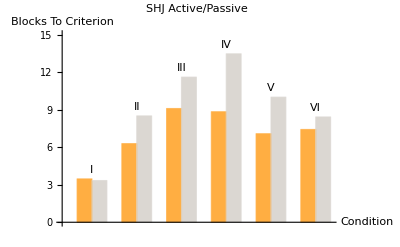
-Graphics--Graphics- | Active
-Graphics- | Passive

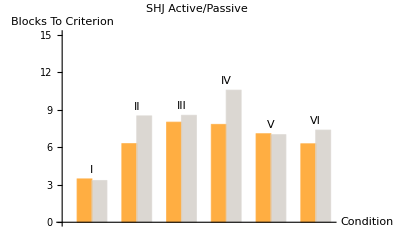
-Graphics--Graphics- | Active
-Graphics- | Passive

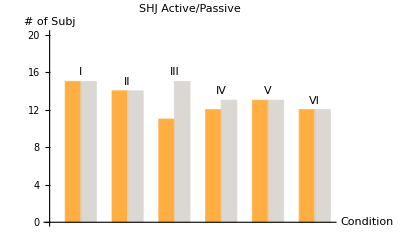
-Graphics--Graphics- | Active
-Graphics- | Passive

```mathematica
BarChart[
Transpose[{getMeanBlocks[active,#-1]&/@Range[6],
getMeanBlocks[passive,#-1]&/@Range[6]}],
PlotRange->{0,15},
ChartLabels->{Placed[{"I","II","III","IV","V","VI"},Above],None},
ChartStyle->{ColorData["Crayola"]["YellowOrange"],
ColorData["Crayola"]["Timberwolf"]},BarSpacing->{0,1},PlotLabel->"SHJ Active/Passive",AxesLabel->{"Condition","Blocks To Criterion"},ChartLegends->{"Active","Passive"}
]


BarChart[
Transpose[{getMeanBlocks2[active,#-1]&/@Range[6],
getMeanBlocks2[passive,#-1]&/@Range[6]}],
PlotRange->{0,15},
ChartLabels->{Placed[{"I","II","III","IV","V","VI"},Above],None},
ChartStyle->{ColorData["Crayola"]["YellowOrange"],
ColorData["Crayola"]["Timberwolf"]},BarSpacing->{0,1},PlotLabel->"SHJ Active/Passive",AxesLabel->{"Condition","Blocks To Criterion"},ChartLegends->{"Active","Passive"}
]

BarChart[
Transpose[{getNSubj[active,#-1]&/@Range[6],
getNSubj[passive,#-1]&/@Range[6]}],
PlotRange->{0,20},
ChartLabels->{Placed[{"I","II","III","IV","V","VI"},Above],None},
ChartStyle->{ColorData["Crayola"]["YellowOrange"],
ColorData["Crayola"]["Timberwolf"]},BarSpacing->{0,1},PlotLabel->"SHJ Active/Passive",AxesLabel->{"Condition","# of Subj"},ChartLegends->{"Active","Passive"}
]
```

## Learning Curve

```mathematica
lcurves=Sort[getLCurve/@fns2v2];
activelcurve=GatherBy[Select[lcurves,#[[1,1]]==0&],First];
passivelcurve=GatherBy[Select[lcurves,#[[1,1]]==1&],First];
```

```mathematica
problemsv1=getAverageLCurve[passivelcurve,#-1]&/@Range[6];
```

```mathematica
problemsv2=getAverageLCurve[passivelcurve,#-1]&/@Range[6];
```

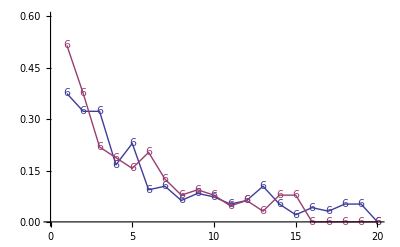

```mathematica
ListPlot[{problemsv1[[-1]],problemsv2[[-1]]},Joined->True,PlotRange->{0,0.6},PlotMarkers->{"6"}]
```

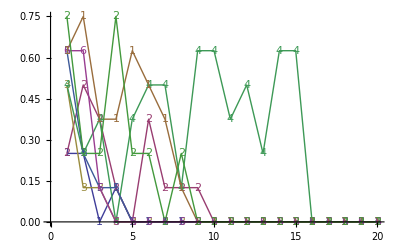

```mathematica
ListPlot[Transpose[lcurves][[-1]],Joined->True,PlotMarkers->{"1","2","3","4","5","6"}]
```

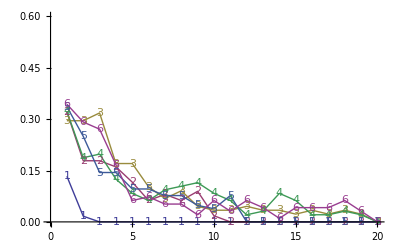

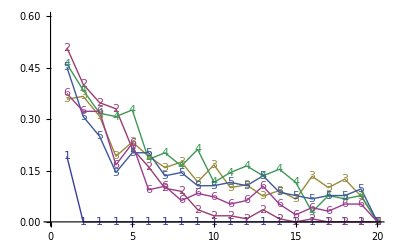

```mathematica
lcurves=Sort[getLCurve/@fns2];
activelcurve=GatherBy[Select[lcurves,#[[1,1]]==0&],First];
passivelcurve=GatherBy[Select[lcurves,#[[1,1]]==1&],First];

problems=getAverageLCurve[activelcurve,#-1]&/@Range[6];
ListPlot[problems,Joined->True,PlotRange->{0,0.6},PlotMarkers->{"1","2","3","4","5","6"}]
problems=getAverageLCurve[passivelcurve,#-1]&/@Range[6];
ListPlot[problems,Joined->True,PlotRange->{0,0.6},PlotMarkers->{"1","2","3","4","5","6"}]
```

## Attrition

```mathematica
droppedout=SQLSelect[conn,"participants_v2",
{"cond"},(SQLColumn["endhit"]==Null)&&(SQLColumn["beginexp"]≠Null)];

all=SQLSelect[conn,"participants_v2",
{"cond"},(SQLColumn["beginexp"]≠Null)];

Sort[Tally[Flatten[droppedout]]]
droppedoutcount=#[[2]]&/@Sort[Tally[Flatten[droppedout]]]
allcount=#[[2]]&/@Sort[Tally[Flatten[all]]];

BarChart[N[droppedoutcount/allcount]]
```

{{1,7},{2,9},{3,6},{4,9},{5,8},{6,1},{7,6},{8,9},{9,10},{10,6},{11,14}}

{7,9,6,9,8,1,6,9,10,6,14}

BarChart[{7.,9.,6.,9.,8.,1.,6.,9.,10.,6.,14.} {0.0666667,0.0454545,0.0416667,0.05,0.0434783,0.0454545,0.0625,0.047619,0.0416667,0.0416667,0.05,0.0357143}]

```mathematica
Sort[Tally[Flatten[droppedout]]]
```

{{1,4},{2,2},{3,6},{4,6},{5,1},{6,1},{7,5},{8,6},{9,4},{10,6},{11,10}}

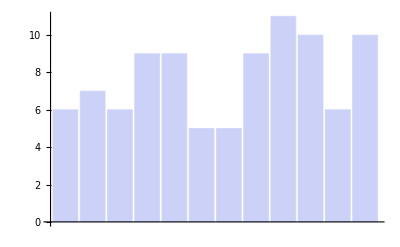

{6,7,6,9,9,5,5,9,11,10,6,10}

```mathematica
BarChart[#[[2]]&/@Sort[Tally[Flatten[res2]]]]
```

```mathematica
BarChart[]
```

-Graphics-